```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsNEW=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-111.txt"}]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

# Diagram 130 (Basis1-111)

```mathematica
PureIntegralsNEW[[130]]
```

hxb[0,0,1,1,0,0,1,1,0,0,0,0,0]

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[3]+p[4];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[1]=ep^3/LS*1/PR[3]
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s345 | 0
1 | mt2-s345 | 0 | -s34
1 | 0 | -s34 | 0)

1/(2 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])

(2 ep^3 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])/PR[3]

# Diagram 132 (Basis1-111)

```mathematica
PureIntegralsNEW[[132]]
```

hxb[0,0,1,1,0,1,0,1,0,0,0,0,0]

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[4]+p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[2]=ep^3/LS*1/PR[3]
```

(0 | 1 | 1 | 1
1 | 0 | mt2-s345 | 0
1 | mt2-s345 | 2 mt2 | mt2-s45
1 | 0 | mt2-s45 | 0)

1/(2 root[s345^2-2 s345 s45+s45^2])

(2 ep^3 root[s345^2-2 s345 s45+s45^2])/PR[3]

# Diagram 136 (Basis1-111)

```mathematica
PureIntegralsNEW[[136]]
```

hxb[0,1,0,1,0,0,1,1,0,0,0,0,0]

```mathematica
q[1]=p[1]+p[6]/.p4cons;
q[2]=p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[3]=ep^3/LS*1/PR[2]
```

(0 | 1 | 1 | 1
1 | 0 | mt2-s16 | -s234
1 | mt2-s16 | 2 mt2 | 0
1 | -s234 | 0 | 0)

1/(2 root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2])

(2 ep^3 root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2])/PR[2]

# Diagram 155 (Basis1 - 111)

```mathematica
PureIntegralsNEW[[155]]
```

hxb[1,0,0,1,0,0,1,1,0,0,0,0,0]

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[6]/.p4cons;
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->mt2,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[4]=ep^3/LS*1/PR[1]
```

(0 | 1 | 1 | 1
1 | 0 | 0 | -s56
1 | 0 | 2 mt2 | 0
1 | -s56 | 0 | 0)

1/(2 root[-4 mt2 s56+s56^2])

(2 ep^3 root[-4 mt2 s56+s56^2])/PR[1]

```mathematica
PureIntegralsTriBubble=PureIntegralsNEW[[{7,8,10,75,76,77,78,79,130,132,136,155}]];
PureIntegralsTriBubble[[9]]=PureIntegralsTriBubble[[9]]*BasisChange[1]
PureIntegralsTriBubble[[10]]=PureIntegralsTriBubble[[10]]*BasisChange[2]
PureIntegralsTriBubble[[11]]=PureIntegralsTriBubble[[11]]*BasisChange[3]
PureIntegralsTriBubble[[12]]=PureIntegralsTriBubble[[12]]*BasisChange[4]
Newsqrts=(Cases[PureIntegralsTriBubble,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[sqrtSet,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"TriBubblePureInts.txt"}],PureIntegralsTriBubble];
```

2 ep^3 hxb[0,0,2,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

2 ep^3 hxb[0,0,2,1,0,1,0,1,0,0,0,0,0] root[s345^2-2 s345 s45+s45^2]

2 ep^3 hxb[0,2,0,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2]

2 ep^3 hxb[2,0,0,1,0,0,1,1,0,0,0,0,0] root[-4 mt2 s56+s56^2]

{mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,-4 mt2 s56+s56^2}

```mathematica
PureIntegralsTriBubble
```

{((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[1,0,0,1,0,0,1,0,0,0,0,0,0])/s56,((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,0,1,1,0,0,1,0,0,0,0,0,0])/s34,((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,1,0,1,0,0,1,0,0,0,0,0,0])/s234,(2 ep^2 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)-(13 ep^3 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)+(27 ep^4 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2)-(18 ep^5 hxb[1,0,0,1,0,0,0,1,0,0,0,0,0])/((1-4 ep) mt2),ep^2 s16 hxb[0,2,0,1,0,0,0,2,0,0,0,0,0],2 ep^2 mt2 hxb[0,2,0,1,0,0,0,2,0,0,0,0,0]+ep^2 mt2 hxb[0,2,0,2,0,0,0,1,0,0,0,0,0]-ep^2 s16 hxb[0,2,0,2,0,0,0,1,0,0,0,0,0],ep^2 s345 hxb[0,0,2,1,0,0,0,2,0,0,0,0,0],2 ep^2 mt2 hxb[0,0,2,1,0,0,0,2,0,0,0,0,0]+ep^2 mt2 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0]-ep^2 s345 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0],2 ep^3 hxb[0,0,2,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2],2 ep^3 hxb[0,0,2,1,0,1,0,1,0,0,0,0,0] root[s345^2-2 s345 s45+s45^2],2 ep^3 hxb[0,2,0,1,0,0,1,1,0,0,0,0,0] root[mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2],2 ep^3 hxb[2,0,0,1,0,0,1,1,0,0,0,0,0] root[-4 mt2 s56+s56^2]}

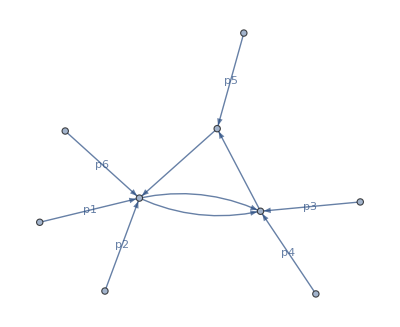

```mathematica
plotDiagram[hxb[0,0,2,1,0,0,1,1,0,0,0,0,0]]
```

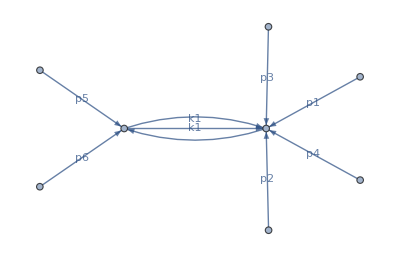

```mathematica
plotDiagram[hxb[1,0,0,1,0,0,1,0,0,0,0,0,0]]
```

```mathematica
PureIntegralsTriBubble[[8]]
```

2 ep^2 mt2 hxb[0,0,2,1,0,0,0,2,0,0,0,0,0]+ep^2 mt2 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0]-ep^2 s345 hxb[0,0,2,2,0,0,0,1,0,0,0,0,0]

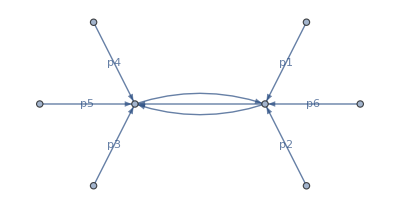

```mathematica
plotDiagram[hxb[0,0,2,2,0,0,0,1,0,0,0,0,0]]
```

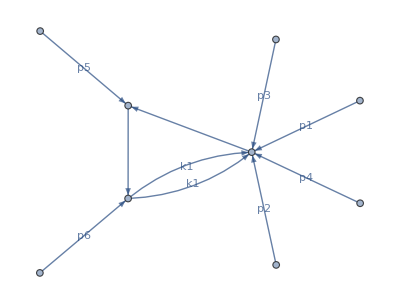

```mathematica
plotDiagram[hxb[2,0,0,1,0,0,1,1,0,0,0,0,0]]
```